z = z0 = 0 is waist of Gaussian beam before the lens;
z = z1 is position of first lens;
z = z2 is final propagating distance;

Improvements needed :
  - handle different waists in x and y;
  - handle astigmatism;
  - put all relevant input parameters at top so all can be changed in one place;

## Before Lens 1

### Initial values (radius of curvature and beam radius just before entering first lens)

Define a longitudinal position for the waist of the incoming beam, z0, which will set our entire coordinate system.

```mathematica
Clear[lambda,z0,w0,beforelens]
Needs["PlotLegends`"]
z0 =-0.861; (*[meters] define longitudinal position of incoming beam waist*)
lambda=1064*10^-9; (* laser wavelength *)
w0 = 1.64*10^-3; (* beam waist *)
zR=π*w0^2/lambda; (* Rayleigh range *)
beforelens[z_]:=N[w0*√(1+(z-z0)^2*lambda/zR^2)] (* incoming beam size as a function of z *)
```

Calculate the radius of curvature, the beam size, and the complex beam parameter, all just before the lens.  Check that inverting the complex beam parameter gives back the same values for radius of curvature and beam size as when those quantities are calculated directly.

```mathematica
Clear[qbeforelensinverse,lensR,lensW,z1,zlens1]
z1=1.016; (* distance from waist, z0, to lens 1 *)
zlens1=z0+z1; (* position of lens 1 in lab coordinate system *)
lensR = N[z1*(1+zR^2/z1^2)] (* radius of curvature at lens 1 *)
lensW = N[w0*√(1+z1^2/zR^2)] (* size of beam at lens 1 *)
qbeforelensinverse=1/lensR-(ⅈ*lambda)/(π*lensW^2);
testlensR=1/Re[qbeforelensinverse] (* radius of curvature at lens 1 *)
testlensW=√(lambda/(π*Im[qbeforelensinverse]))(* size of beam at lens 1 *)
```

63.0883

0.00165337

63.0883

0.+0.00165337 ⅈ

Then, back-propagate by the distance z1 to make sure I get the original waist value back.

```mathematica
qatwaist=1/qbeforelensinverse-z1; (* complex beam parameter at waist *)
testwaist=√((lambda*Im[qatwaist])/π)(* waist of original beam *)
```

0.00164

Sweet!

## Lens 1

### Propagation through the lens (at position z >= z1)

```mathematica
Clear[afterlensR,afterlensW,f]
f = 500*10^-3; (* focal length of lens *)
afterlensW=lensW (* size of beam directly after lens 1; same as right before lens 1 *)
afterlensR=1/(1/lensR-1/f) (* radius of curvature of beam after lens 1 *)
```

0.00165337

-0.503994

Doing the same calculation in the complex parameter formalism:

```mathematica
Clear[qafterlensinverse]
qafterlensinverse = qbeforelensinverse-1/f;(* inverse complex beam parameter after lens 1 *)
afterlensR = 1/Re[qafterlensinverse] (* radius of curvature of beam after lens 1 *)
```

-0.503994

It matches, as it should.

### What is new waist value and location after lens?

```mathematica
afterlenswaistz=N[f/(1+(f/zR)^2)] (* relative position of waist of beam after lens 1 *)
afterlenswaist=N[(f*lambda)/(π*w0)*√(1/(1+(f/zR)^2))] (* size of waist after lens 1 *)
```

0.498026

0.000103053

Doing the same in the complex parameter formalism:

```mathematica
Clear[qwaist]
qwaist=1/qafterlensinverse+afterlenswaistz;(* complex beam parameter, at waist, after lens 1 *)
afterlenswaist=√((lambda*Im[qwaist])/π)(* size of waist after lens 1 *)
(*afterlens2waistz=Abs[Re[qwaist2]]*)
```

0.000103039

This again matches between the formula and the derived complex parameter.  Good; I have more confidence that I am calculating the new waist value correctly.

Now, calculate the new Rayleigh range:

```mathematica
Clear[afterlenszR]
afterlenszR=π*afterlenswaist^2/lambda
```

0.0313483

### Final propagation to position z = z2

Free space propagation of beam after lens 1

```mathematica
Clear[afterlens]
afterlens[z_]:= N[afterlenswaist*√(1+((z-(zlens1+afterlenswaistz))/afterlenszR)^2)](* size of beam after lens 1 as a function of z *)
```

The second lens is distance z2 away from the waist of the beam between the lenses.  Determine radius of curvature, beam size, and complex beam parameter at the position of lens 2.

```mathematica
Clear[z2,qlens2,qlens2inverse,lens2R,lens2W]
z2=0.9; (* distance from afterbeamwaistz to lens 2 *)
zlens2=zlens1+afterlenswaistz+z2;(* position of lens 2 in lab coordinate system *)
qlens2=qwaist+z2;(* complex beam parameter at lens 2; distance added is that from waist after lens 1 to position of lens 2 *)
qlens2inverse=1/qlens2; (* inverse complex beam parameter at lens 2 *)
lens2R=1/Re[qlens2inverse] ;(* radius of curvature of post-lens 1 beam at lens 2 *)
lens2W= N[afterlenswaist*√(1+(z2/afterlenszR)^2)];
(* size of post-lens 1 beam at lens 2 *)
```

## Lens 2

### Propagation through the second lens (at position z >= z2)

Place a second lens (f2 = 250 mm ) 250 mm away from waist of post-lens1 beam.  This should be a telescope configuration which should halve the size of the original input beam.

```mathematica
Clear[afterlens2R,afterlens2W,f2]
f2 = 300*10^-3; (* focal length of lens *)
afterlens2W=lens2W (* size of beam directly after lens 2 *)
afterlens2R=1/(1/lens2R-1/f2)
(* radius of curvature of beam directly after lens 2 *)
```

0.00296002

-0.450732

Doing the same calculation in the complex parameter formalism:

```mathematica
Clear[qafterlens2inverse]
qafterlens2inverse = qlens2inverse-1/f2;
afterlens2R = 1/Re[qafterlens2inverse]
```

-0.450732

It matches, as it should.

### What is new waist value and location after lens 2?

These two formulas are not correct? or at least an approximation doesn't hold that means they're off by a bit?

```mathematica
afterlens2waistzA=N[f2/(1+(f2/afterlenszR)^2)]
afterlens2waist=N[(f2*lambda)/(π*afterlenswaist)*√(1/(1+(f2/afterlenszR)^2))]
```

0.00324034

0.000102481

Doing the same in the complex parameter formalism:

```mathematica
Clear[qwaist2]
qwaist2=1/qafterlens2inverse+afterlens2waistzA
afterlens2waist=√((lambda*Im[qwaist2])/π)
afterlens2waistz=Abs[Re[qwaist2]]
```

-0.447353+0.00792101 ⅈ

0.0000517948

0.447353

The formula and the complex beam parameter only roughly match.  I think this is because zR is not much greater than the focal length.  The waist obtained from the complex beam parameter is correct.

Now, calculate the new Rayleigh range:

```mathematica
Clear[afterlens2zR]
afterlens2zR=π*afterlens2waist^2/lambda
```

0.00792101

### Final propagation to position z = z3

Free space propagation of beam after lens 2.

```mathematica
Clear[afterlens2,finalR]
afterlens2[z_]:= N[afterlens2waist*√(1+((z-(zlens2+afterlens2waistz))/afterlens2zR)^2)]
finalR[z_]:=N[(z-(zlens2+afterlens2waistz))*(1+afterlens2zR^2/(z-(zlens2+afterlens2waistz))^2)]
```

```mathematica
afterlens2[zlens2+1]
```

0.00361408

## Plot waist sizes before and after lenses

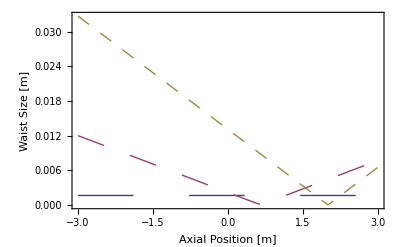

```mathematica
Plot[{beforelens[z],afterlens[z],afterlens2[z]},{z,-3,3},PlotStyle->{{Thick,Dashing[0.1]},{Thick,Dashing[0.05]},{Thick,Dashing[0.025]}},Frame->True,FrameStyle->Directive[Bold,16],FrameLabel->{"Axial Position [m]","Waist Size [m]","Beam Propagation Through a Lens",""},PlotLegend->{"Before Lens","After Lens 1","After Lens 2"},LegendPosition->{1.0,-0.3}]
```

## Real Beam Propagation

```mathematica
z0 =0; (* define longitudinal position of incoming beam waist *)
lambda=1064*10^-9; (* laser wavelength *)
wreal=0.005; (* real beam size in meters *)
Msq = 1.1; (* beam quality parameter; how close to ideal is laser beam *)
zRreal=π*wreal^2/(Msq*lambda); (* Rayleigh range *)

realbeamsize[z_]:=N[wreal*√(1+(z-z0)^2/zRreal^2)]
```

```mathematica
dist=1;
beforelens[dist]
realbeamsize[dist]
```

0.00164

0.00500056